```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
(*Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergInstaSWAPGerardCZ.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)*)
Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP Windows Vers.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
(*Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm*)
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

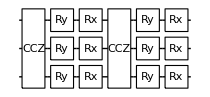
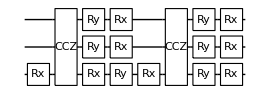
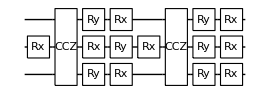
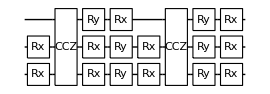
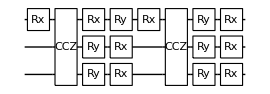
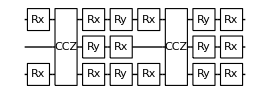
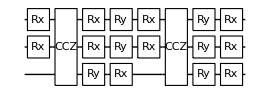
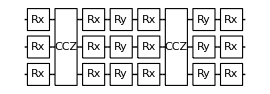

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0.945313,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125},{0.0078125,0.945313,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125},{0.0078125,0.0078125,0.945313,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125},{0.0078125,0.0078125,0.0078125,0.945313,0.0078125,0.0078125,0.0078125,0.0078125},{0.0078125,0.0078125,0.0078125,0.0078125,0.945313,0.0078125,0.0078125,0.0078125},{0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.945313,0.0078125,0.0078125},{0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.945313,0.0078125},{0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.0078125,0.945313}}

```mathematica
InitCirc[NQ_]:=Table[Subscript[Init, b],{b,0,NQ-1,1}]
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed],1]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
Table[DrawCircuit[GroverIteration3Q[KetList[3][[i]]]],{i,1,8}]
KetList[3]
GroversAlg3Q=Table[SearchSeeds=KetList[3];
ρ=CreateDensityQureg[3];
(*InitZeroState[ρ];*)
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[InitCirc[3],HTrans[0],HTrans[1],HTrans[2]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,InitialisationCirc];
Gr=ExtractCircuit[GetCircuitSchedule[GroverIteration3Q[SearchSeeds[[i]]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,Join[Gr,Gr]];CalcProbOfAllOutcomes[ρ,{0,1,2}],{i,1,8}]

DestroyAllQuregs[];
```

```mathematica
?CalcProbOfAllOutcomes
```

```mathematica
{{0.7812500000000003,0.9453125000000011,0.3300781250000008,0.14111328125000047,0.5479736328125018,0.9997863769531297,0.5769729614257846},{0.7690906524658252,0.8858532905578675,0.5292235612869307,0.9679377377033318,0.6609973385930126,0.6607868243008923,0.9680651244707513},{0.643413705867723,0.8168076086149192,0.8706407575009626,0.6201202025131445,0.9537010694771346,0.7031355487726048,0.7335910856855166},{0.5838071130662745,0.7827738645598313,0.6338757380272025,0.653451853877103,0.7720166979325492,0.5791553612793856,0.7519921422259972},{0.4787273414903013,0.7202226972274148,0.6221987416442911,0.5210429530233975,0.7781722226863981,0.5021733808583934,0.6538055613002676},{0.3723738422255659,0.6525746663025611,0.5037935831168199,0.4346010663753844,0.6940416614574689,0.38795428721487923,0.5842442671222673},{0.42553273961777494,0.568325900229838,0.40779331364974347,0.353650515747961,0.6291352578228634,0.4002782054793187,0.4838207996042885},{0.620310642296595,0.47092433682033963,0.3827598910868513,0.5076134730653771,0.5374888376457083,0.5839244660711629,0.37638528943880334}}
```

{{0.78125,0.945313,0.330078,0.141113,0.547974,0.999786,0.576973},{0.769091,0.885853,0.529224,0.967938,0.660997,0.660787,0.968065},{0.643414,0.816808,0.870641,0.62012,0.953701,0.703136,0.733591},{0.583807,0.782774,0.633876,0.653452,0.772017,0.579155,0.751992},{0.478727,0.720223,0.622199,0.521043,0.778172,0.502173,0.653806},{0.372374,0.652575,0.503794,0.434601,0.694042,0.387954,0.584244},{0.425533,0.568326,0.407793,0.353651,0.629135,0.400278,0.483821},{0.620311,0.470924,0.38276,0.507613,0.537489,0.583924,0.376385}}

```mathematica
ExtractCircuit[GetCircuitSchedule[{Subscript[CCZ, 0,1,2]},RydDev,ReplaceAliases->True]]
CalcCircuitMatrix[ExtractCircuit[GetCircuitSchedule[Flatten[{XTrans[0],XTrans[1],XTrans[2],Subscript[CCZ, 0,1,2],XTrans[0],XTrans[1],XTrans[2]}],RydDev,ReplaceAliases->True]]]//MatrixForm
(-1/ⅈ)^3*CalcCircuitMatrix[Join[HTrans[0],HTrans[1],HTrans[2]]]-CalcCircuitMatrix[{Subscript[H, 0],Subscript[H, 1],Subscript[H, 2]}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

(-(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2)
-(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

{{-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm},{-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,-1/(2 √2)+MatrixForm,1/(2 √2)+MatrixForm}}[{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)}}]

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)}}

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

{U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
ToffSandBread[t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```

```mathematica
N[2*Sqrt[2]]
```

2.82843

```mathematica
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[{InitCirc[3]},{HTrans[0],HTrans[1],HTrans[2]}],RydDev,ReplaceAliases->True]]
```

{Ry_0[π/2],Rx_0[π],Ry_1[π/2],Rx_1[π],Ry_2[π/2],Rx_2[π]}

```mathematica
Grover2Q11=ExtractCircuit[GetCircuitSchedule[{Subscript[H, 0],Subscript[H, 1],Subscript[Rz, 0][Pi],Subscript[Rz, 1][Pi],Subscript[CZG, 0,1],Subscript[H, 0],Subscript[H, 1],Subscript[CZG, 0,1],Subscript[H, 0],Subscript[H, 1](*,Subscript[Rz, 0][Pi],Subscript[Rz, 1][Pi],Subscript[CZG, 0,1],Subscript[H, 0],Subscript[H, 1],Subscript[CZG, 0,1],Subscript[H, 0],Subscript[H, 1]*)},RydDev,ReplaceAliases->True]]
```

{H_0,H_1,Rz_0[π],Rz_1[π],U_(0,1)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],H_0,H_1,U_(0,1)[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],H_0,H_1}

```mathematica
Reg=CreateDensityQureg[2];
InitZeroState[Reg]
ApplyCircuit[Reg,Grover2Q11]
CalcProbOfAllOutcomes[Reg,{0,1}]
```

22

{}

{0.,0.,0.,1.}

```mathematica
Toff[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
```

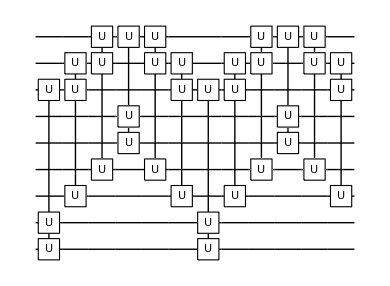

32

```mathematica
C5ZMat=DiagonalMatrix[Join[{1},Table[-1,{i,1,2^5-1}]]];
C5XCirc={Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2],Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2]};
DrawCircuit[C5XCirc]
Length[C5ZMat]
```